# MA2330

## 5.7 Ordinary Differential Equations: x'=A x

The 2D linear ODE system x'=A x means 
	x_1' | = | a_11 x_1 | + | a_12 x_2
x_2' | = | a_21 x_1 | + | a_22 x_2
It should be clear what this means in high dimensions!  Solutions are functions that satisfy the equation!

The weighted sum z(t)=c_1 x(t)+c_2 y(t) of two solutions x(t) and y(t) is also a solution since 
	z'(t)=c_1 x'(t)+c_2 y'(t)=c_1(A x(t))+c_2(A y(t))=A (c_1 x(t)+c_2 y(t))=A z(t).

ODE texts show that there are always n linearly independent solutions of x'=A x in n dimensions.  A basis for the set of solutions is a  fundamental set of solutions. An Initial Value Problem (IVP) selects the unique solution satisfying x(t_0)=x_o.  A fundamental matrix Φ(t) has columns from a fundamental set of solutions. Note
	Φ'(t)=(y_1' | y_2' | … | y_n')=(A y_1 | A y_2 | … | A y_n)=A (y_1 | y_2 | … | y_n)=A Φ(t)  
Since the columns of Φ are a basis any solution x(t) has 
	x(t)=c_1 y_1(t)+…+c_n y_n(t)=Φ(t) (c_1
⋮
c_n)=Φ(t) c
and the solution to the IVP x(t_0)=x_0 is 
	 x(t)=Φ(t) c 
where the constants c are computed by solving Φ(t_0)c=x_0.

### Diagonalization: A=P D P^-1

If x'=A x then 
	x'=P D P^-1 x=P D (P^-1 x) ⟺ P^-1x'=P^-1 P D (P^-1 x)
and 
	(P^-1 x)'= D (P^-1 x) ⟺ y'=D y.
for diagonalizable matrices A the behavior of x'=A x is determined by the eigenvalues of A.

### Real Eigenvalues - (λ_1 | 0 0 | λ_2)

The system  
	(x_1
x_2)' | = | (λ_1 | 0
0 | λ_2) (x_1
x_2)
is simply 
	x_1' | =
x_2' | = | λ_1 x_1
λ_2 x_2
which has solutions 
	x_1 | =
x_2 | = | c_1 ⅇ^(λ_1 t)
c_2 ⅇ^(λ_2 t)
and a fundamental matrix is 
	Φ(t)=(ⅇ^(λ_1 t) | 0
0 | ⅇ^(λ_2 t)).

Both solutions grow if λ_1>0 and λ_2>0. “Repeller”

Both solutions decay to zero if λ_1<0 and λ_2<0. “Attractor”

One solution grows and the other decays if λ_1 λ_2<0. “Saddle”

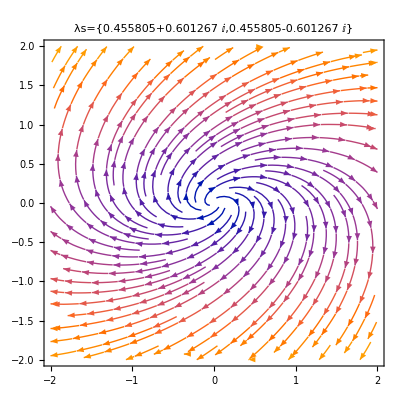

```mathematica
A=RandomReal[{-1,1},{2,2}];
StreamPlot[A.{x1,x2},{x1,-2,2},{x2,-2,2},
PlotLabel->StringForm["λs=``",Eigenvalues[A]]]
```

### Complex Eigenvalues λ=a ±b ⅈ

We have a choice of matrices (a | -b
b | a) or (a+ b ⅈ | 0
0 | a-b ⅈ).  The system
	(x_1
x_2)' | = | (a | -b
b | a) (x_1
x_2)
does not look much better when written out
	x_1' | =
x_2' | = | a x_1-b x_2
b x_1+a x_2
so we are stuck with trying to understand the complex diagonal system
	x_1' | =
x_2' | = | (a+b ⅈ) x_1
(a-b ⅈ) x_1
which has the “formal” solution
	x_1 | =
x_2 | = | c_1 ⅇ^((a+b ⅈ)t) | = | c_1∑_(k=0)^∞ (((a+b ⅈ)t)^k/k!)
c_2 ⅇ^((a-b ⅈ)t) | = | c_2∑_(k=0)^∞ (((a-b ⅈ)t)^k/k!)
because 
	e^z | =1+z+z^2/(2!)+z^3/(3!)+… | =∑_(k=0)^∞ (z^k/k!) 
The traditional way (in the book on p325-326) to get rid of the complex numbers is to work out that
	ⅇ^((a+b ⅈ)t)=ⅇ^(a t +b t ⅈ)=ⅇ^(a t+ b t ⅈ)=ⅇ^(a t) ⅇ^(b t ⅈ)=ⅇ^(a t) ∑_(k=0)^∞ (b t)^k ⅈ^k
you can split the sum up into even and odd terms
	ⅇ^((a+b ⅈ)t)=ⅇ^(a t)ⅇ^((b ⅈ)t)=ⅇ^(a t) ∑_(k=1)^∞ (b t)^k ⅈ^k=ⅇ^(a t) (∑_(j=0)^∞ (b t)^(2j)ⅈ^(2j)+∑_(j=0)^∞ (b t)^(2j+1)ⅈ^(2j+1))
and look for the pattern in the complex powers
	ⅈ^0 | = | 1
ⅈ^1 | = | ⅈ
ⅈ^2 | = | -1
ⅈ^3 | = | -ⅈ
ⅈ^4 | = | 1
ⅈ^5 | = | ⅈ
ⅈ^6 | = | -1
ⅈ^7 | = | -ⅈ
ⅈ^8 | = | 1
to get 
	ⅇ^((a+b ⅈ)t)=ⅇ^(a t) (∑_(j=0)^∞ (b t)^(2j)(-1)^j+ⅈ ∑_(j=0)^∞ (b t)^(2j+1)(-1)^j)
The last step is to recognize the series for cosine and sine to get
	ⅇ^((a+b ⅈ)t)=ⅇ^(a t) (cos(b t)+ⅈ sin(b t))
and naturally the conjugate version is 
	 ⅇ^((a-b ⅈ)t)=ⅇ^(a t) (cos(b t)-ⅈ sin(b t)).

If you plug this (with λ=a+ⅈ b and v=re(v)+ⅈ im(v)) into the solution form you get 
	   v ⅇ^((a+b ⅈ)t)=ⅇ^(a t) (cos(b t)+ⅈ sin(b t))(re(v)+ⅈ im(v))
which expands to
	 (re(v)+ⅈ im(v)) ⅇ^((a+b ⅈ)t)=ⅇ^(a t) (cos(b t) re(v)+ⅈ sin(b t) re(v)+ⅈ cos(b t)im(v) + ⅈ^2 sin(b t) im(v))
which tidies up to 
	 (re(v)+ⅈ im(v)) ⅇ^((a+b ⅈ)t)=ⅇ^(a t) (cos(b t) re(v)-sin(b t) im(v)) +ⅈ ⅇ^(a t) (sin(b t) re(v)+cos(b t)im(v)) 
The complex conjugate gives 
	 (re(v)-ⅈ im(v)) ⅇ^((a-b ⅈ)t)=ⅇ^(a t) (cos(b t) re(v)-sin(b t) im(v)) -ⅈ ⅇ^(a t) (sin(b t) re(v)+cos(b t)im(v)) 
The real and imaginary bits give the two real linearly independent solutions
	y_1= ⅇ^(a t) (cos(b t) re(v)-sin(b t) im(v)) 
y_2= ⅇ^(a t) (sin(b t) re(v)+cos(b t) im(v))

### Pictures of ODEs

StreamPlot and StreamPlot3D plot solutions of Dynamical Systems in 2 or 3 dimensions.

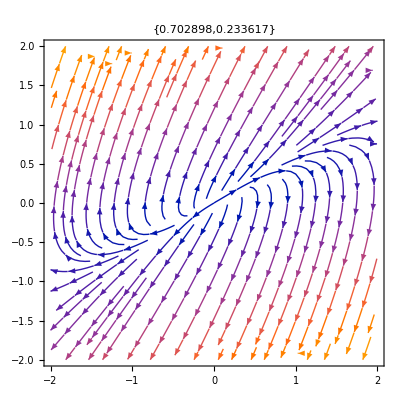

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];
StreamPlot[ A.{x1,x2},{x1,-2,2},{x2,-2,2},
PlotLabel->Eigenvalues[A]]
```

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];
StreamPlot3D[ A.{x1,x2,x3},{x1,-2,2},{x2,-2,2},{x3,-2,2},
PlotLabel->Eigenvalues[A]]
```

-Graphics3D-

## Summary

As a consequence of the diagonalization theorem.

Evals of A give the long time behavior of the Dynamical System x'=A x

Complex evals a± b ⅈ are spirals in the re(v)—im(v) plane.

They spiral in if a<0 and out if a>0.

They spin fast if b is big and slow if b is small

Real evals λ are attracting directions if λ<0 and repelling directions if λ>0.